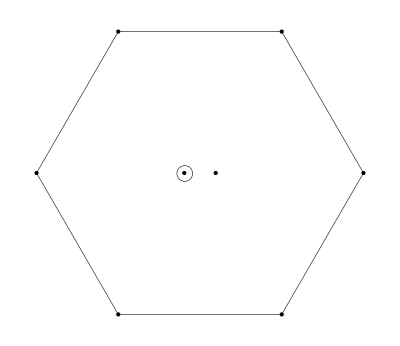

Y=0,  I_3=0

(ud-du)(d̄ū-ūd̄)+(us-su)(ūs̄-s̄ū)

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C(γ̄)^5 u_b-u_a^T C(γ̄)^5 d_b) ((d̄)_a(γ̄)^5 C((ū)_b)^T)+(u_a^T C(γ̄)^5 d_b-d_a^T C(γ̄)^5 u_b) ((ū)_a(γ̄)^5 C((d̄)_b)^T)+(u_a^T C(γ̄)^5 d_b) ((d̄)_b(γ̄)^5 C((ū)_a)^T-(ū)_b(γ̄)^5 C((d̄)_a)^T)+(d_a^T C(γ̄)^5 u_b) ((ū)_b(γ̄)^5 C((d̄)_a)^T-(d̄)_b(γ̄)^5 C((ū)_a)^T)+(u_a^T C(γ̄)^5 s_b) ((s̄)_a(γ̄)^5 C((ū)_b)^T-(s̄)_b(γ̄)^5 C((ū)_a)^T)+(s_a^T C(γ̄)^5 u_b-u_a^T C(γ̄)^5 s_b) ((ū)_a(γ̄)^5 C((s̄)_b)^T)+(s_a^T C(γ̄)^5 u_b) ((s̄)_b(γ̄)^5 C((ū)_a)^T-(ū)_b(γ̄)^5 C((s̄)_a)^T)-s_a^T C(γ̄)^5 u_b(s̄)_a(γ̄)^5 C((ū)_b)^T+u_a^T C(γ̄)^5 s_b(ū)_b(γ̄)^5 C((s̄)_a)^T

the Fierz rearranged J (to naively get the decay partten)

```mathematica
(ū(γ̄)^5 u) (s̄(γ̄)^5 s-d̄(γ̄)^5 d)+(ū 1u) (s̄ 1s-d̄ 1d)-d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u+d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d-d̄ γ^μ d ū γ^μ u+d̄ γ^μ u ū γ^μ d+d̄(γ̄)^5 u ū(γ̄)^5 d+1/2 (d̄ σ^μν d ū σ^μν u)-1/2 (d̄ σ^μν u ū σ^μν d)+d̄ 1u ū 1d+s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u-s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s+s̄ γ^μ s ū γ^μ u-s̄ γ^μ u ū γ^μ s-s̄(γ̄)^5 u ū(γ̄)^5 s-1/2 (s̄ σ^μν s ū σ^μν u)+1/2 (s̄ σ^μν u ū σ^μν s)-s̄ 1u ū 1s
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(1920 π^6)-(⟨ GG ⟩ log(-q^2/μ^2) q^4)/(48 π^5)-(⟨ d̄ d⟩ log(-q^2/μ^2) (m_d-2 m_u) q^4)/(12 π^4)-(⟨ s̄ s⟩ log(-q^2/μ^2) (m_s-2 m_u) q^4)/(12 π^4)+(⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s-m_u) q^4)/(6 π^4)-(⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(6 π^2)-(⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(6 π^2)-(⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(⟨G^3⟩ log(-q^2/μ^2) q^2)/(216 π^6)+(⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(4 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(4 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(13 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(72 π^2)+(13 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(72 π^2)+(⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(13 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(72 π^2)-(13 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(72 π^2)+(⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2+(⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(13 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(36 π^2)-(⟨ GG ⟩ ⟨ d̄ d⟩^2)/(18 π q^2)-(⟨ GG ⟩ ⟨ s̄ s⟩^2)/(18 π q^2)-(⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-⟨ d̄ Gd⟩^2/(96 π^2 q^2)-⟨ s̄ Gs⟩^2/(96 π^2 q^2)-⟨ ū Gu⟩^2/(48 π^2 q^2)+(⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)-(2 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)-(2 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)+(⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(48 π^2 q^2)-(59 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(288 π^2 q^2)-(59 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(288 π^2 q^2)-(2 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (8 m_d-10 m_u))/(9 q^2)-(2 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (8 m_s-10 m_u))/(9 q^2)+(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ m_u)/(3 q^2)-(2 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (8 m_u-10 m_d))/(9 q^2)-(2 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (8 m_u-10 m_s))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

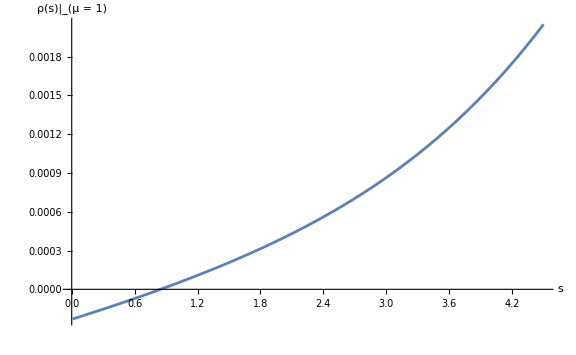
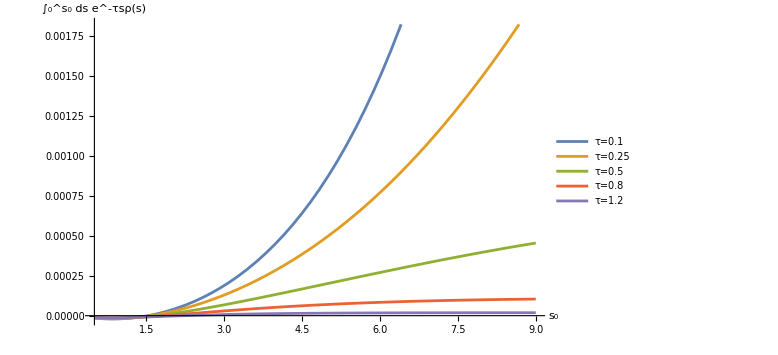

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

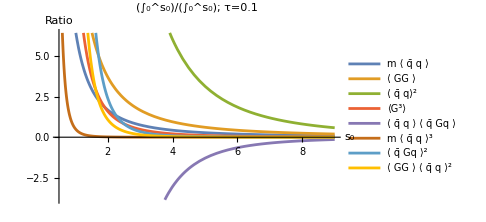
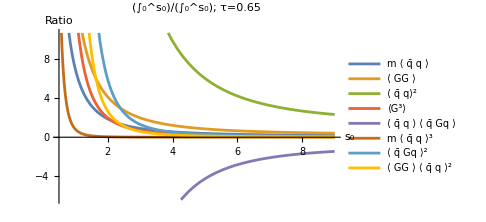
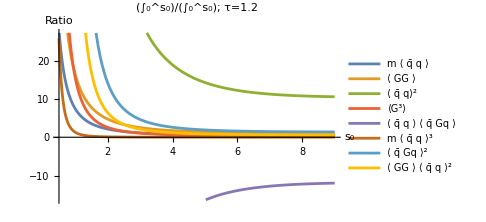

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

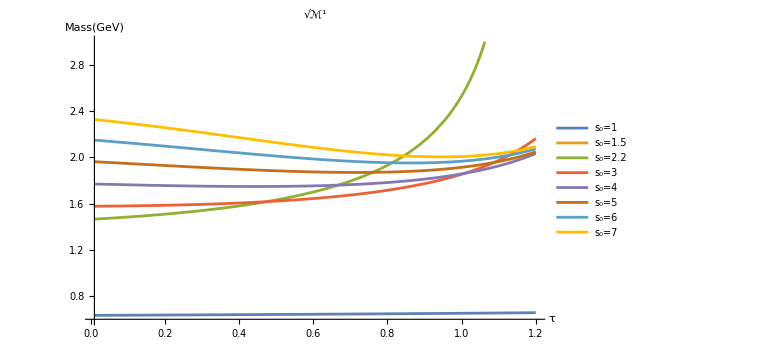
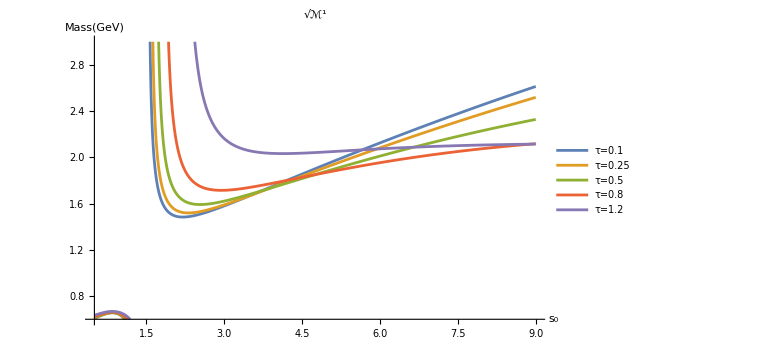

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

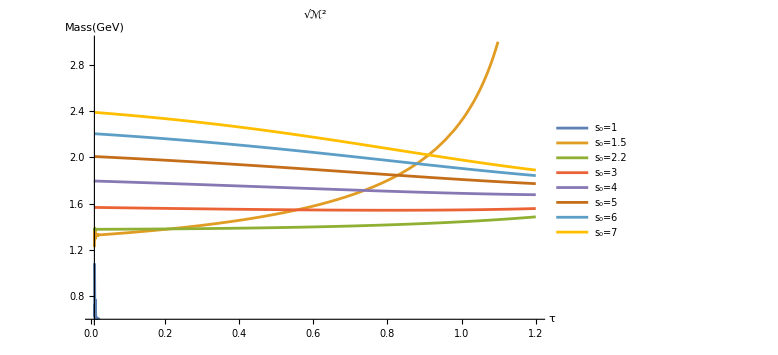
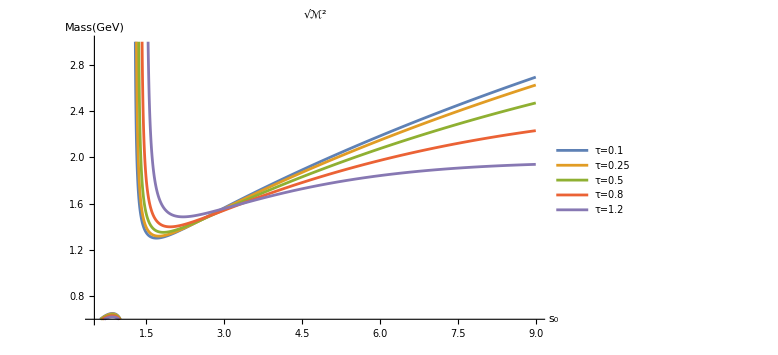

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

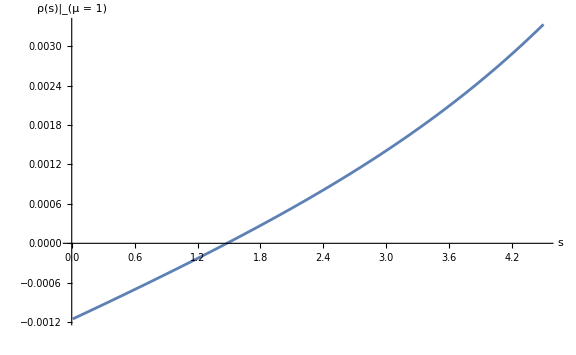
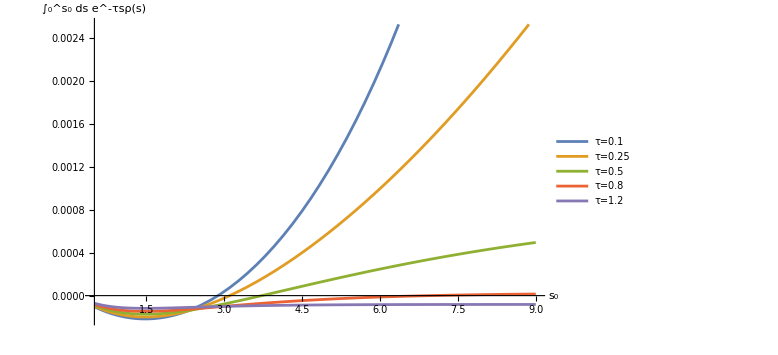

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

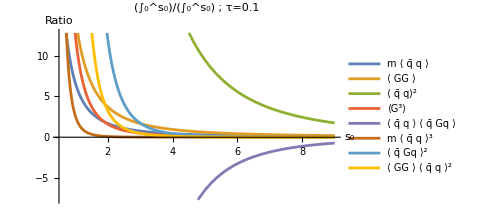
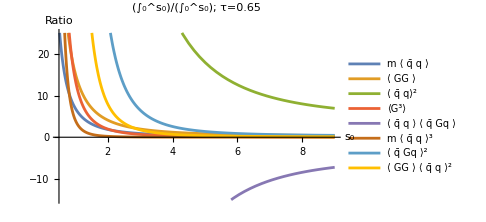
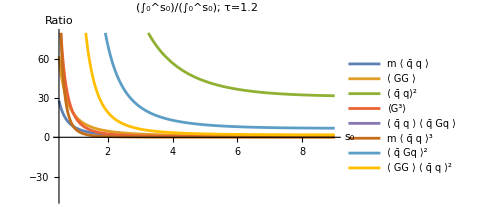

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

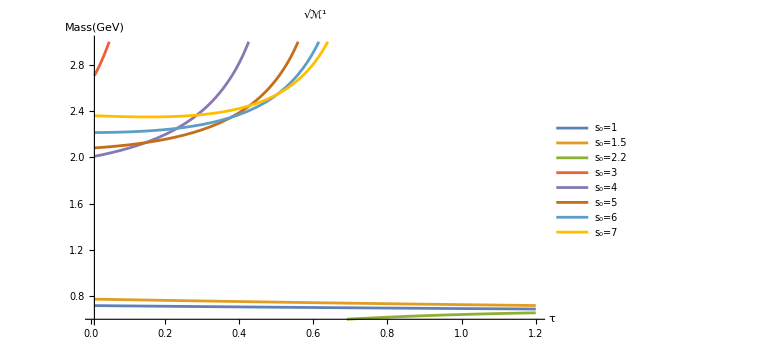
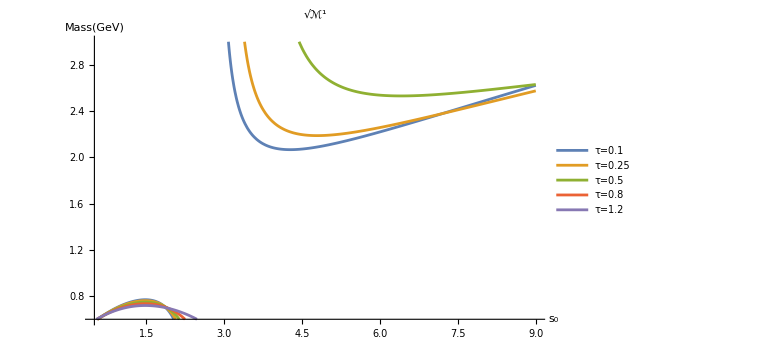

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5